```mathematica
fd[agent_, amount_Real]:=Replace[agent, <|head___, "position"->x_,tail___ |> -> <|head, "position"->AngleVector[x,{amount, agent[["heading"]]}], tail|>]
```

```mathematica
rt[agent_, amount_Integer]:= Replace[agent, <|head___, "heading"->x_,tail___ |> -> <|head, "heading"-> (Mod[agent[["heading"]]- (amount °), 360])°, tail|>]
```

```mathematica
setup=Table[<|"position"->RandomReal[{-0.1,0.1},2],"heading"->RandomInteger[{0, 360}]° |>,{100}];
```

```mathematica
display[agents_]:=
ListPlot[#[["position"]]& /@ agents,
ImageSize->400,
PlotMarkers->{-Graphics3D-},
GridLines->{Range[-2, 2,0.25],Range[-2, 2,0.25]},
AspectRatio->1,
Frame->True,
Axes->False,
PlotRange->{{-2,2},{-2,2}}
];
```

```mathematica
simulate[f_,init_,viz_]:=Dynamic@ Manipulate[
Refresh[
If[goForever||tick,
t++;
tick=False;
turtles=f[turtles]
];
TableForm[{"ticks: "<>ToString[t],viz[turtles]},TableAlignments->Right]
,UpdateInterval->If[goForever,0,Infinity]
],
{{t,0},ControlType->None},
{{turtles,init},ControlType->None},
{{tick,False},ControlType->None},
{{goForever,False,"go (loop)"},{True,False}},
Button["go once",tick=True],
Button["setup",goForever=False;turtles=init;t=0],
SynchronousUpdating->True,
SaveDefinitions->True
];
```

```mathematica
go[agents_]:=rt[fd[#, RandomReal[]],RandomInteger[{-10, 10}]] &/@agents;
```

```mathematica
simulate[go,setup,display]
```

```mathematica
$turtles
```

{}

```mathematica
Manipulate[Graphics[Line[{{0,0},p}],PlotRange->2],{{p,{1,1}},Locator}]
```

```mathematica
Turtle[x_Dynamic]:=Echo[x]
Turtle[Dynamic[{{0,1}, canvas}]]
```

```mathematica
$Turtles[[Length[$Turtles]+1]]
```

Part::partw: Part 101 of {{0.521961,0.65299},{0.56126,0.496736},{0.357422,0.893286},{0.494313,0.217851},«43»,{0.532479,0.450062},{0.418975,0.563435},{0.264942,0.707802},«50»} does not exist.

{{0.521961,0.65299},{0.56126,0.496736},{0.357422,0.893286},{0.494313,0.217851},{0.644942,0.76026},{0.0634363,0.116608},{0.033116,0.396697},{0.583717,0.86785},{0.582241,0.174891},{0.309783,0.900377},{0.236927,0.310086},{0.098013,0.0677983},{0.149556,0.44948},{0.634687,0.565224},{0.0776924,0.917906},{0.622274,0.782731},{0.0682819,0.131167},{0.643593,0.0438593},{0.295234,0.646355},{0.448145,0.587113},{0.395801,0.519952},{0.686054,0.711901},{0.729603,0.874603},{0.555067,0.74244},{0.58663,0.861847},{0.2647,0.320079},{0.73525,0.801529},{0.655347,0.877633},{0.926091,0.3666},{0.586762,0.711916},{0.730683,0.696196},{0.311741,0.622787},{0.643347,0.669304},{0.532197,0.0325605},{0.697937,0.00513372},{0.723459,0.598376},{0.764147,0.724708},{0.742075,0.775091},{0.775136,0.768596},{0.630065,0.750212},{0.501632,0.256464},{0.694309,0.809834},{0.698305,0.796941},{0.659585,0.712381},{0.0445169,0.352165},{0.556738,0.697014},{0.814582,0.168285},{0.532479,0.450062},{0.418975,0.563435},{0.264942,0.707802},{0.636497,0.773168},{0.34348,0.850306},{0.309591,0.264499},{0.531878,0.846174},{0.71965,0.81343},{0.0297773,0.149929},{0.73026,0.873778},{0.275006,0.693594},{0.656233,0.036339},{0.246671,0.205658},{0.659325,0.843827},{0.760964,0.702309},{0.73223,0.738468},{0.462948,0.821857},{0.667788,0.43436},{0.363368,0.714459},{0.938873,0.15712},{0.141126,0.19122},{0.446667,0.781845},{0.559898,0.0294812},{0.67478,0.654494},{0.645186,0.825057},{0.63171,0.00671686},{0.439678,0.866286},{0.794515,0.293497},{0.517566,0.668282},{0.464581,0.456883},{0.722916,0.710321},{0.624355,0.851858},{0.593568,0.764082},{0.681641,0.849663},{0.0428508,0.990428},{0.34632,0.543539},{0.481016,0.433136},{0.475067,0.710212},{0.974008,0.363355},{0.332166,0.0801196},{0.772329,0.783851},{0.190919,0.12453},{0.716838,0.782569},{0.789996,0.114786},{0.468509,0.897732},{0.699993,0.823849},{0.309357,0.126116},{0.154274,0.118103},{0.510021,0.77786},{0.237691,0.394647},{0.639429,0.728593},{0.443195,0.859838},{0.496181,0.12327}}⟦101⟧

```mathematica
$Turtles
```

{{0.521961,0.65299},{0.56126,0.496736},{0.357422,0.893286},{0.494313,0.217851},{0.644942,0.76026},{0.0634363,0.116608},{0.033116,0.396697},{0.583717,0.86785},{0.582241,0.174891},{0.309783,0.900377},{0.236927,0.310086},{0.098013,0.0677983},{0.149556,0.44948},{0.634687,0.565224},{0.0776924,0.917906},{0.622274,0.782731},{0.0682819,0.131167},{0.643593,0.0438593},{0.295234,0.646355},{0.448145,0.587113},{0.395801,0.519952},{0.686054,0.711901},{0.729603,0.874603},{0.555067,0.74244},{0.58663,0.861847},{0.2647,0.320079},{0.73525,0.801529},{0.655347,0.877633},{0.926091,0.3666},{0.586762,0.711916},{0.730683,0.696196},{0.311741,0.622787},{0.643347,0.669304},{0.532197,0.0325605},{0.697937,0.00513372},{0.723459,0.598376},{0.764147,0.724708},{0.742075,0.775091},{0.775136,0.768596},{0.630065,0.750212},{0.501632,0.256464},{0.694309,0.809834},{0.698305,0.796941},{0.659585,0.712381},{0.0445169,0.352165},{0.556738,0.697014},{0.814582,0.168285},{0.532479,0.450062},{0.418975,0.563435},{0.264942,0.707802},{0.636497,0.773168},{0.34348,0.850306},{0.309591,0.264499},{0.531878,0.846174},{0.71965,0.81343},{0.0297773,0.149929},{0.73026,0.873778},{0.275006,0.693594},{0.656233,0.036339},{0.246671,0.205658},{0.659325,0.843827},{0.760964,0.702309},{0.73223,0.738468},{0.462948,0.821857},{0.667788,0.43436},{0.363368,0.714459},{0.938873,0.15712},{0.141126,0.19122},{0.446667,0.781845},{0.559898,0.0294812},{0.67478,0.654494},{0.645186,0.825057},{0.63171,0.00671686},{0.439678,0.866286},{0.794515,0.293497},{0.517566,0.668282},{0.464581,0.456883},{0.722916,0.710321},{0.624355,0.851858},{0.593568,0.764082},{0.681641,0.849663},{0.0428508,0.990428},{0.34632,0.543539},{0.481016,0.433136},{0.475067,0.710212},{0.974008,0.363355},{0.332166,0.0801196},{0.772329,0.783851},{0.190919,0.12453},{0.716838,0.782569},{0.789996,0.114786},{0.468509,0.897732},{0.699993,0.823849},{0.309357,0.126116},{0.154274,0.118103},{0.510021,0.77786},{0.237691,0.394647},{0.639429,0.728593},{0.443195,0.859838},{0.496181,0.12327}}

```mathematica
$Turtles = Table[RandomReal[{0, 1},2], 100];
Dynamic[Graphics[Function[self,Locator[Dynamic[$Turtles[[self]],Function[value,$Turtles[[self]]=value;
Function[index,$Turtles[[index]]+=.1 (
($Turtles[[If[index - 1 ==0, Length[$Turtles],index - 1] ]]/2)-($Turtles[[If[index + 1 == Length[$Turtles] + 1, 1, index + 1]]]/2)
)]/@
Position[$Turtles,x_List/;0<EuclideanDistance[x,value]<1,{1}]]]]]/@Range[Length[$Turtles]
]], UpdateInterval->Infinity, TrackedSymbols->{}]
```

```mathematica
turtle[pos_, heading_, task_]:= Graphics[Locator[]]
```

```mathematica
turtle[{0,0}, 0, Function[
```

```mathematica
Graphics
```

```mathematica
rotate=AnglePath[{0,0},{{4,45°},{3 √2,-45°}},"FrameAngle"]
```

{0,45 °,0}

```mathematica
turtle=-Graphics-
```

-Graphics-

```mathematica
FullForm[turtle]
```

Graphics[List[List[RGBColor[0.598322,0.291997,0.0727092],Opacity[1],EdgeForm[List[GrayLevel[0],Opacity[0.],CapForm["Round"]]],Polygon[List[List[-0.6075,-0.3375],List[-0.7425,-0.4125],List[-0.7575,-0.4725],List[-0.8025,-0.5175],List[-0.8025,-0.5475],List[-0.8025,-0.5775],List[-0.7875,-0.5925],List[-0.7575,-0.5775],List[-0.7575,-0.6075],List[-0.7425,-0.6375],List[-0.7875,-0.6525],List[-0.7725,-0.6675],List[-0.7275,-0.6675],List[-0.6975,-0.6525],List[-0.6675,-0.6525],List[-0.6825,-0.6825],List[-0.6975,-0.6975],List[-0.6825,-0.7125],List[-0.6525,-0.6825],List[-0.6225,-0.6375],List[-0.6075,-0.6675],List[-0.6225,-0.6975],List[-0.6075,-0.7125],List[-0.5775,-0.6675],List[-0.5775,-0.6375],List[-0.5625,-0.5925],List[-0.5625,-0.5625],List[-0.5625,-0.5325],List[-0.4875,-0.4575]]],Polygon[List[List[-0.555,0.3875],List[-0.69,0.4625],List[-0.705,0.5225],List[-0.75,0.5675],List[-0.75,0.5975],List[-0.75,0.6275],List[-0.735,0.6425],List[-0.705,0.6275],List[-0.705,0.6575],List[-0.69,0.6875],List[-0.735,0.7025],List[-0.72,0.7175],List[-0.675,0.7175],List[-0.645,0.7025],List[-0.615,0.7025],List[-0.63,0.7325],List[-0.645,0.7475],List[-0.63,0.7625],List[-0.6,0.7325],List[-0.57,0.6875],List[-0.555,0.7175],List[-0.57,0.7475],List[-0.555,0.7625],List[-0.525,0.7175],List[-0.525,0.6875],List[-0.51,0.6425],List[-0.51,0.6125],List[-0.51,0.5825],List[-0.435,0.5075]]],Polygon[List[List[0.5875,-0.105],List[0.7075,-0.135],List[0.8425,-0.15],List[0.9025,-0.12],List[0.9925,-0.12],List[1.0375,-0.075],List[1.0375,-0.045],List[1.0825,-0.015],List[1.0825,0.015],List[1.0375,0.045],List[1.0375,0.075],List[0.9925,0.12],List[0.9025,0.12],List[0.8425,0.15],List[0.7075,0.135],List[0.5875,0.105]]],Polygon[List[List[0.54,-0.325],List[0.6,-0.4],List[0.615,-0.445],List[0.6,-0.49],List[0.57,-0.565],List[0.57,-0.58],List[0.585,-0.61],List[0.57,-0.625],List[0.585,-0.67],List[0.555,-0.7],List[0.555,-0.73],List[0.51,-0.76],List[0.51,-0.745],List[0.525,-0.73],List[0.51,-0.715],List[0.495,-0.745],List[0.465,-0.775],List[0.435,-0.775],List[0.435,-0.76],List[0.465,-0.745],List[0.465,-0.715],List[0.45,-0.7],List[0.435,-0.715],List[0.405,-0.73],List[0.375,-0.73],List[0.375,-0.715],List[0.405,-0.715],List[0.435,-0.685],List[0.405,-0.655],List[0.405,-0.625],List[0.435,-0.565],List[0.42,-0.55],List[0.42,-0.52],List[0.45,-0.475],List[0.42,-0.445]]],Polygon[List[List[0.4,0.4],List[0.46,0.475],List[0.475,0.52],List[0.46,0.565],List[0.43,0.64],List[0.43,0.655],List[0.445,0.685],List[0.43,0.7],List[0.445,0.745],List[0.415,0.775],List[0.415,0.805],List[0.37,0.835],List[0.37,0.82],List[0.385,0.805],List[0.37,0.79],List[0.355,0.82],List[0.325,0.85],List[0.295,0.85],List[0.295,0.835],List[0.325,0.82],List[0.325,0.79],List[0.31,0.775],List[0.295,0.79],List[0.265,0.805],List[0.235,0.805],List[0.235,0.79],List[0.265,0.79],List[0.295,0.76],List[0.265,0.73],List[0.265,0.7],List[0.295,0.64],List[0.28,0.625],List[0.28,0.595],List[0.31,0.55],List[0.28,0.52]]]],List[RGBColor[0.253803,0.451667,0.0323796],Opacity[1],EdgeForm[List[RGBColor[0.0629435,0.315663,0.00775158],Opacity[1],CapForm["Round"]]],FilledCurve[List[BSplineCurve[List[List[0.6,0.],List[0.6,-0.45],List[-0.1,-0.65],List[-0.6,-0.5],List[-0.75,0.],List[-0.6,0.5],List[-0.1,0.65],List[0.6,0.45]],Rule[SplineClosed,True]]]]],List[RGBColor[0.351522,0.54258,0.0562448],Opacity[1.],EdgeForm[List[RGBColor[0.546,0.702,0.028],Opacity[1],CapForm["Round"]]],FilledCurve[List[BSplineCurve[List[List[0.5,0.],List[0.5,-0.35],List[-0.1,-0.5],List[-0.5,-0.4],List[-0.6,0.],List[-0.5,0.4],List[-0.1,0.5],List[0.5,0.35]],Rule[SplineClosed,True]]]]],List[RGBColor[0.546,0.702,0.028],Opacity[1],CapForm["Round"],Arrowheads[Medium],Line[List[List[-0.125,-0.25],List[-0.155,-0.46]]],Line[List[List[-0.4,0.125],List[-0.55,0.15]]],Line[List[List[-0.4,-0.125],List[-0.55,-0.15]]],Line[List[List[0.5,0.],List[-0.565,0.]]],Line[List[List[-0.375,0.225],List[-0.475,0.325]]],Line[List[List[-0.375,-0.225],List[-0.475,-0.325]]],Line[List[List[-0.25,-0.175],List[-0.375,-0.225],List[-0.425,0.],List[-0.375,0.225],List[-0.25,0.175]]],Line[List[List[0.,-0.175],List[-0.125,-0.25],List[-0.25,-0.175],List[-0.25,0.175],List[-0.125,0.25],List[0.,0.175]]],Line[List[List[0.25,-0.1],List[0.15,-0.25],List[0.,-0.175],List[0.,0.175],List[0.15,0.25],List[0.25,0.1]]],Line[List[List[0.475,-0.2],List[0.25,-0.1],List[0.25,0.1],List[0.475,0.2]]],Line[List[List[0.15,-0.25],List[0.205,-0.41]]],Line[List[List[-0.125,0.25],List[-0.15,0.455]]],Line[List[List[0.15,0.25],List[0.205,0.41]]]]],Rule[ImageSize,50]]

```mathematica
turtle={-Graphics-, 0, 0};
```

```mathematica
turtle[[3]]
```

0

-Graphics-

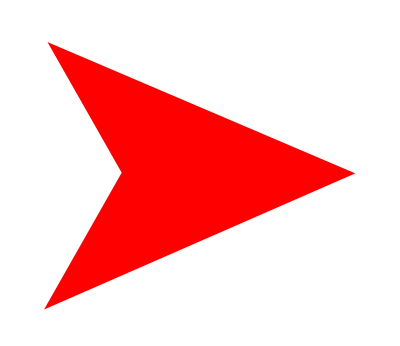
```mathematica
Style[-Graphics-, 0.5]
```

-Graphics-

```mathematica
Graphics[Style[List[EdgeForm[List[Opacity[0.],CapForm["Round"]]],FaceForm[RGBColor[1,0,0]],Polygon[List[List[-0.7759950791541192,0.8247210514369927],List[-0.3304072086136789,0.039307784571650295],List[-0.7967772616818327,-0.7834878720632044],List[1.072629538072977,0.03534927361399065]]]],Rule[ImagePadding,List[List[0.,1.],List[1.,0.]]],Rule[PlotRange,List[List[-0.8417708333333334,1.1217708333333334],List[-0.8127,0.8876999999999999]]],Rule[PlotRangePadding,Automatic]], ImageSize\[Rule]1]
```

```mathematica
Tiny
```

Tiny

```mathematica
Clear[turtle]
turtle={{0,0}, 0,-Graphics-, <|"test"->5|>};
```

```mathematica
$Turtles = Table[{i,RandomInteger[10, 2], 0,-Graphics-, <|"test"->5|>}, {i, 10}]
```

{{1,{7,3},0,-Graphics-,<|test→5|>},{2,{1,4},0,-Graphics-,<|test→5|>},{3,{2,0},0,-Graphics-,<|test→5|>},{4,{0,8},0,-Graphics-,<|test→5|>},{5,{7,2},0,-Graphics-,<|test→5|>},{6,{0,5},0,-Graphics-,<|test→5|>},{7,{8,7},0,-Graphics-,<|test→5|>},{8,{4,7},0,-Graphics-,<|test→5|>},{9,{8,4},0,-Graphics-,<|test→5|>},{10,{4,7},0,-Graphics-,<|test→5|>}}

```mathematica
DynamicModule[{steps={},path,points},
Manipulate[
path=AnglePath[{0.,0.},steps,{"Position","FrameMatrix"}];points=path[[All,1]]; $Turtles[[who]][[1]] = Last[points];
Graphics[{
Line[points],GeometricTransformation[turtle[[3]][[1]],AffineTransform[{path[[-1,2]].RotationMatrix[θ],Last[points]}]],
White, Point[{{-25,-25},{25,25}}]},
Axes->False,
PlotRange->All
],
Row[{Control[{{who,1},0,100}]}],
Row[{Control[{{r,1},0,10}]}],
Row[{Control[{{θ,0},-Pi,Pi}]}],
Button["go-once",AppendTo[steps,{r,θ}];turtle[[2]] = turtle[[2]] + θ; θ=0.;],
Button["setup",{steps={},r=1.,θ=0.}]
]
]
```

```mathematica
DynamicModule[{steps={},path,points},
Manipulate[
path=AnglePath[{0.,0.},steps,{"Position","FrameMatrix"}];points=path[[All,1]]; $Turtles[[who]][[1]] = Last[points];
Graphics[{
Line[points],GeometricTransformation[turtle[[3]][[1]],AffineTransform[{path[[-1,2]].RotationMatrix[θ],Last[points]}]],
White, Point[{{-25,-25},{25,25}}]},
Axes->False,
PlotRange->All
],
Row[{Control[{{who,1},0,100}]}],
Row[{Control[{{r,1},0,10}]}],
Row[{Control[{{θ,0},-Pi,Pi}]}],
Button["go-once",AppendTo[$Turtles[[who]][[6]],{r,θ}];turtle[[2]] = turtle[[2]] + θ; θ=0.;],
Button["setup",{steps={},r=1.,θ=0.}]
]
]
```